```mathematica
散射的程序
```

```mathematica
波函数的对数的导数连续
```

```mathematica
ψ1=a1*ⅇ^(ⅈ*α*x)+a2*ⅇ^(-ⅈ*α*x);
ψ2=b1*ⅇ^(β*x)+b2*ⅇ^(-β*x);
ψ3=c1*ⅇ^(ⅈ*α*x)+c2*ⅇ^(-ⅈ*α*x);
ψ4=d1*ⅇ^(β*x)+d2*ⅇ^(-β*x);
ψ5=f1*ⅇ^(ⅈ*α*x);
(D[Log[ψ1],x]/.x->0)==D[Log[ψ2],x]/.x->0
(D[Log[ψ2],x]/.x->b)==D[Log[ψ3],x]/.x->b
(D[Log[ψ3],x]/.x->b+w)==D[Log[ψ4],x]/.x->b+w
(D[Log[ψ4],x]/.x->2b+w)==D[Log[ψ5],x]/.x->2b+w
Clear[ψ1,ψ2,ψ3,ψ4,ψ5]
```

((ⅈ a1 π)/3-(ⅈ a2 π)/3)/(a1+a2)==(b1 β-b2 β)/(b1+b2)

(-b2 ⅇ^(-b β) β+b1 ⅇ^(b β) β)/(b2 ⅇ^(-b β)+b1 ⅇ^(b β))==(-1/3 ⅈ c2 ⅇ^(-1/3 ⅈ b π) π+1/3 ⅈ c1 ⅇ^((ⅈ b π)/3) π)/(c2 ⅇ^(-1/3 ⅈ b π)+c1 ⅇ^((ⅈ b π)/3))

(-1/3 ⅈ c2 ⅇ^(-1/3 ⅈ (50+b) π) π+1/3 ⅈ c1 ⅇ^(1/3 ⅈ (50+b) π) π)/(c2 ⅇ^(-1/3 ⅈ (50+b) π)+c1 ⅇ^(1/3 ⅈ (50+b) π))==(-d2 ⅇ^(-(50+b) β) β+d1 ⅇ^((50+b) β) β)/(d2 ⅇ^(-(50+b) β)+d1 ⅇ^((50+b) β))

(-d2 ⅇ^(-(50+2 b) β) β+d1 ⅇ^((50+2 b) β) β)/(d2 ⅇ^(-(50+2 b) β)+d1 ⅇ^((50+2 b) β))==(ⅈ π)/3

```mathematica
求比值k
```

```mathematica
Solve[(- ⅇ^(-(2 b+w) β) β+k1 ⅇ^((2 b+w) β) β)/(ⅇ^(-(2 b+w) β)+k1 ⅇ^((2 b+w) β))==ⅈ α,k1]
```

Solve::ivar: 0.996195 is not a valid variable.

Solve[{(-ⅇ^((-50-2 b) β) β+0.996195 ⅇ^((50+2 b) β) β)/(ⅇ^((-50-2 b) β)+0.996195 ⅇ^((50+2 b) β)),(-ⅇ^((-50-2 b) β) β+0.0871557 ⅇ^((50+2 b) β) β)/(ⅇ^((-50-2 b) β)+0.0871557 ⅇ^((50+2 b) β))}==(ⅈ π)/3,{0.996195,0.0871557}]

```mathematica
Solve[(-ⅈ  ⅇ^(-ⅈ (b+w) α) α+ⅈ k2 ⅇ^(ⅈ (b+w) α) α)/(ⅇ^(-ⅈ (b+w) α)+k2 ⅇ^(ⅈ (b+w) α))==
((- ⅇ^(-(b+w) β) β+k1 ⅇ^((b+w) β) β)/(ⅇ^(-(b+w) β)+k1 ⅇ^((b+w) β))/.k1->-(ⅇ^(2 (-2 b-w) β) (α-ⅈ β))/(α+ⅈ β)),
k2]//FullSimplify
```

Solve::ivar: 0.989931 is not a valid variable.

Solve[{((0.-1.0472 ⅈ)+(0.897768-0.518326 ⅈ) ⅇ^((2 ⅈ b π)/3))/(1.-(0.494965+0.857305 ⅈ) ⅇ^((2 ⅈ b π)/3)),((0.-1.0472 ⅈ)-(0.128375-0.0741175 ⅈ) ⅇ^((2 ⅈ b π)/3))/(1.+(0.070777+0.122589 ⅈ) ⅇ^((2 ⅈ b π)/3))}=={(1.+1/(-0.5-0.498097 ⅇ^(2 (50+b) β))) β,(1.+1/(-0.5-0.0435779 ⅇ^(2 (50+b) β))) β},{0.989931,-0.141554}]

```mathematica
Solve[(- ⅇ^(-b β) β+k3 ⅇ^(b β) β)/(ⅇ^(-b β)+k3 ⅇ^(b β))==
((-ⅈ  ⅇ^(-ⅈ b α) α+ⅈ k2 ⅇ^(ⅈ b α) α)/(ⅇ^(-ⅈ b α)+k2 ⅇ^(ⅈ b α))/.
k2->(ⅇ^(-2 ⅈ (b+w) α) (α^2-β^2+2 ⅈ α β Coth[b β]))/(α^2+β^2)),k3]//
FullSimplify
```

{}

```mathematica
Solve[(ⅈ k4 α-ⅈ  α)/(k4+1)==
((k3 β- β)/(k3+1)/.
k3->
(ⅇ^(-2 b β) (α-ⅈ β) 
(2 ⅈ α β Cosh[b β]+(α^2-ⅇ^(2 ⅈ w α) (α+ⅈ β)^2-β^2) 
Sinh[b β]))/
((α+ⅈ β) 
(-2 ⅈ α β Cosh[b β]+
(-α^2+ⅇ^(2 ⅈ w α) (α-ⅈ β)^2+β^2) Sinh[b β]))),
k4]//FullSimplify
```

{{k4→(24 (-1)^(2/3) π β (π^2-9 β^2) Cosh[b β]-9 π^2 β^2 (3 ⅈ+√3+(ⅈ+3 √3) Cosh[2 b β]) Csch[b β]+(3 ⅈ+√3) (π^4+81 β^4) Sinh[b β])/((6+6 ⅈ √3) π β (π^2+9 β^2) Cosh[b β]+(3 ⅈ+√3) (π^4-81 β^4) Sinh[b β])}}

```mathematica
波函数在边界连续
```

```mathematica
ψ1=a1*ⅇ^(ⅈ*α*x)+a2*ⅇ^(-ⅈ*α*x);
ψ2=b1*ⅇ^(β*x)+b2*ⅇ^(-β*x);
ψ3=c1*ⅇ^(ⅈ*α*x)+c2*ⅇ^(-ⅈ*α*x);
ψ4=d1*ⅇ^(β*x)+d2*ⅇ^(-β*x);
ψ5=f1*ⅇ^(ⅈ*α*x);
(ψ1/.x->0)==ψ2/.x->0
(ψ2/.x->b)==ψ3/.x->b
(ψ3/.x->b+w)==ψ4/.x->b+w
(ψ4/.x->2b+w)==ψ5/.x->2b+w
Clear[ψ1,ψ2,ψ3,ψ4,ψ5]
```

a1+a2==b1+b2

b2 ⅇ^(-b β)+b1 ⅇ^(b β)==c2 ⅇ^(-1/3 ⅈ b π)+c1 ⅇ^((ⅈ b π)/3)

c2 ⅇ^(-1/3 ⅈ (50+b) π)+c1 ⅇ^(1/3 ⅈ (50+b) π)==d2 ⅇ^(-(50+b) β)+d1 ⅇ^((50+b) β)

d2 ⅇ^(-(50+2 b) β)+d1 ⅇ^((50+2 b) β)==ⅇ^(1/3 ⅈ (50+2 b) π) f1

```mathematica
计算透射系数
```

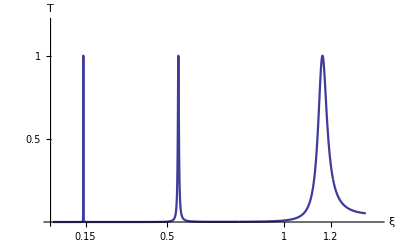

```mathematica
b=2.0;w=5.0;V0=1.355;T={};const=1.32521;
Do[
α=const √ξ;β=const √(V0-ξ);
k1=-(ⅇ^(2 (-2 b-w) β) (α-ⅈ β))/(α+ⅈ β);
k2=(ⅇ^(-2 ⅈ (b+w) α) (α^2-β^2+2 ⅈ α β Coth[b β]))/(α^2+β^2);
k3=(ⅇ^(-2 b β) (α-ⅈ β) 
(2 ⅈ α β Cosh[b β]+(α^2-ⅇ^(2 ⅈ w α) (α+ⅈ β)^2-β^2) 
Sinh[b β]))/((α+ⅈ β) 
(-2 ⅈ α β Cosh[b β]+
(-α^2+ⅇ^(2 ⅈ w α) (α-ⅈ β)^2+β^2) Sinh[b β]));
k4=
(-4 ⅈ α (α-β) β (α+β) Cosh[b β]+4 α^2 β^2 Csch[b β]+
(-α^4+6 α^2 β^2-β^4+ⅇ^(2 ⅈ w α) (α^2+β^2)^2) Sinh[b β])/
(-2 ⅈ (1+ⅇ^(2 ⅈ w α)) α β (α^2+β^2) Cosh[b β]+
(-1+ⅇ^(2 ⅈ w α)) (α^4-β^4) Sinh[b β]);
s=Solve[{1+1/k4==b1+b2,b1==b2*k3},
{b1,b2}];{b1,b2}={b1,b2}/.s[[1]];
s=Solve[{b2 ⅇ^(-b β)+b1 ⅇ^(b β)==c2 ⅇ^(-ⅈ b α)+c1 ⅇ^(ⅈ b α),
c1==c2*k2},{c1,c2}];{c1,c2}={c1,c2}/.s[[1]];
s=
Solve[{c2 ⅇ^(-ⅈ (b+w) α)+c1 ⅇ^(ⅈ (b+w) α)==d2 ⅇ^(-(b+w) β)+d1 ⅇ^((b+w) β),
d1==d2*k1},{d1,d2}];{d1,d2}={d1,d2}/.s[[1]];
s=Solve[d2 ⅇ^(-(2 b+w) β)+d1 ⅇ^((2 b+w) β)==ⅇ^(ⅈ (2 b+w) α) f1,f1];
f1=f1/.s[[1]];AppendTo[T,{ξ,Abs[f1]^2}];
Clear[b1,b2,c1,c2,d1,d2,f1],
{ξ,0.01,1.35,0.00005}]
Export["e:/data/onewell.dat",T];
ListLinePlot[T,PlotRange->{{0,1.4},{0,1.2}},
AxesOrigin->{0,0},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13},AxesLabel->{"ξ","T"},
Ticks->{{0.15,0.5,1,1.2},{0.5,1}}]
Clear[b1,b2,c1,c2,d1,d2,f1]
```

```mathematica
二阱的透射系数计算
```

{2012,2,10,13,34,49.2548828}

NSolve::precw: The precision of the argument function ({(0.0148641  - 0.171777\ ⅈ) - b1 - b2, b1 - (0.00176804  + 4.72673×10^-12\ ⅈ)\ b2}
) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({(0.0012532  - 0.0144826\ ⅈ) - (0.965032  + 0.262133\ ⅈ)\ c1 - (0.965032  - 0.262133\ ⅈ)\ c2, c1 - (0.442568  + 0.896735\ ⅈ)\ c2}
) is less than WorkingPrecision (30).

NSolve::precw: The precision of the argument function ({(0.0001586  - 0.00183286\ ⅈ) - 47383.\ d1 - 0.0000211046\ d2, d1 - (7.87512×10^-13 + 1.84922×10^-17\ ⅈ)\ d2}
) is less than WorkingPrecision (30).

General::stop: Further output of NSolve :: precw will be suppressed during this calculation.

{2012,2,10,13,34,56.6279296}

{2012,2,10,13,35,3.8232421}

{2012,2,10,13,35,11.171875}

{2012,2,10,13,35,18.5761718}

{2012,2,10,13,35,26.118164}

{2012,2,10,13,35,33.5771484}

{2012,2,10,13,35,41.040039}

{2012,2,10,13,35,48.5322265}

{2012,2,10,13,35,56.0371093}

{2012,2,10,13,36,3.5898437}

{2012,2,10,13,36,11.139648}

{2012,2,10,13,36,18.7910156}

{2012,2,10,13,36,26.4736328}

{2012,2,10,13,36,34.1142578}

{2012,2,10,13,36,41.7734375}

{2012,2,10,13,36,49.524414}

{2012,2,10,13,36,57.3076171}

{2012,2,10,13,37,5.0966796}

{2012,2,10,13,37,12.966797}

{2012,2,10,13,37,20.8886718}

{2012,2,10,13,37,28.84375}

{2012,2,10,13,37,36.7919921}

{2012,2,10,13,37,44.8447265}

{2012,2,10,13,37,52.883789}

{2012,2,10,13,38,0.9765625}

{2012,2,10,13,38,9.0810546}

{2012,2,10,13,38,17.236328}

{2012,2,10,13,38,25.3623046}

{2012,2,10,13,38,33.5917968}

{2012,2,10,13,38,41.8300781}

{2012,2,10,13,38,50.1630859}

{2012,2,10,13,38,58.5058593}

{2012,2,10,13,39,6.9287109}

{2012,2,10,13,39,15.325195}

{2012,2,10,13,39,23.8925781}

{2012,2,10,13,39,32.4208984}

{2012,2,10,13,39,40.993164}

{2012,2,10,13,39,49.6386718}

{2012,2,10,13,39,58.3701171}

{2012,2,10,13,40,7.8847656}

{2012,2,10,13,40,17.34668}

{2012,2,10,13,40,26.6240234}

{2012,2,10,13,40,36.1103515}

{2012,2,10,13,40,45.4765625}

{2012,2,10,13,40,54.4873046}

{2012,2,10,13,41,3.5351562}

{2012,2,10,13,41,12.632813}

{2012,2,10,13,41,21.7910156}

{2012,2,10,13,41,30.9912109}

{2012,2,10,13,41,40.2539062}

{2012,2,10,13,41,49.5361328}

{2012,2,10,13,41,58.9648437}

{2012,2,10,13,42,8.5585937}

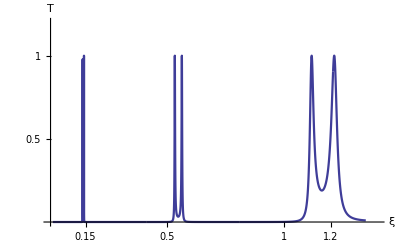

```mathematica
Date[]
mm=1;db=2.;dw=5.;V0=1.355;t={};
Do[
α=1.32616 √ξ;β=1.32616 √(V0-ξ);
k1=-(ⅇ^(2 (-3 db-2 dw) β) (α-ⅈ β))/(α+ⅈ β);
k2=(ⅇ^(-4 ⅈ (db+dw) α) (α^2-β^2+2 ⅈ α β Coth[db β]))/(α^2+β^2);
k3=(ⅇ^(-2 (2 db+dw) β) (ⅇ^(2 ⅈ dw α) (-ⅈ α-β) (α+ⅈ β)^2 Sinh[db β]+(ⅈ α+β) (2 ⅈ α β Cosh[db β]+(α-β) (α+β) Sinh[db β])))/((-ⅈ α+β) (2 ⅈ α β Cosh[db β]+(α^2-ⅇ^(2 ⅈ dw α) (α-ⅈ β)^2-β^2) Sinh[db β]));
k4=(ⅇ^(-2 ⅈ (db+dw) α) (-4 ⅈ α (α-β) β (α+β) Cosh[db β]+4 α^2 β^2 Csch[db β]+(-α^4+6 α^2 β^2-β^4+ⅇ^(2 ⅈ dw α) (α^2+β^2)^2) Sinh[db β]))/(-2 ⅈ (1+ⅇ^(2 ⅈ dw α)) α β (α^2+β^2) Cosh[db β]+(-1+ⅇ^(2 ⅈ dw α)) (α^4-β^4) Sinh[db β]);
k5=(ⅇ^(-2 db β) (α-ⅈ β) (2 α β (ⅇ^(2 ⅈ dw α) (α+ⅈ β)^2+ⅇ^(4 ⅈ dw α) (α+ⅈ β)^2-2 (α-β) (α+β)) Cosh[db β]+ⅈ (-4 α^2 β^2 Csch[db β]+(α^4-6 α^2 β^2+β^4+ⅇ^(4 ⅈ dw α) (α-β) (α+ⅈ β)^2 (α+β)-2 ⅇ^(2 ⅈ dw α) (α+ⅈ β)^2 (α^2-ⅈ α β-β^2)) Sinh[db β])))/((-ⅈ α+β) (-2 ⅈ α β (ⅇ^(2 ⅈ dw α) (α-ⅈ β)^2+ⅇ^(4 ⅈ dw α) (α-ⅈ β)^2-2 (α-β) (α+β)) Cosh[db β]-4 α^2 β^2 Csch[db β]+(α^4-6 α^2 β^2+β^4+ⅇ^(4 ⅈ dw α) (α-β) (α-ⅈ β)^2 (α+β)-2 ⅇ^(2 ⅈ dw α) (α-ⅈ β)^2 (α^2+ⅈ α β-β^2)) Sinh[db β]));
k6=-((α^2+β^2) Sinh[db β] (2 ⅇ^(2 ⅈ dw α) (α^2-β^2)^2-(α^2+β^2)^2-ⅇ^(4 ⅈ dw α) (α^2+β^2)^2+(α^4-6 α^2 β^2+β^4-2 ⅇ^(2 ⅈ dw α) (α^2+β^2)^2+ⅇ^(4 ⅈ dw α) (α^4-6 α^2 β^2+β^4)) Cosh[2 db β]+4 ⅈ (-1+ⅇ^(4 ⅈ dw α)) α β (-α^2+β^2) Sinh[2 db β]))/(4 (4 ⅈ α^3 β^3 Cosh[db β]^3+6 α^2 (α-β) β^2 (α+β) Cosh[db β]^2 Sinh[db β]-ⅈ α β (3 (α^2-β^2)^2-2 ⅇ^(2 ⅈ dw α) (α^2+β^2)^2-ⅇ^(4 ⅈ dw α) (α^2+β^2)^2) Cosh[db β] Sinh[db β]^2-ⅇ^(2 ⅈ dw α) (α-β) (α+β) (-(α^2+β^2)^2+(α^4+β^4) Cos[2 dw α]+2 ⅈ α^2 β^2 Sin[2 dw α]) Sinh[db β]^3));
sol=NSolve[{1+k6==b1+b2,b1==b2*k5},{b1,b2},30];
{b1,b2}={b1,b2}/.sol[[1]];
sol=NSolve[{b2 ⅇ^(-db β)+b1 ⅇ^(db β)==c2 ⅇ^(-ⅈ db α)+c1 ⅇ^(ⅈ db α),c1==c2*k4},{c1,c2},30];
{c1,c2}={c1,c2}/.sol[[1]];
sol=NSolve[{c2 ⅇ^(-ⅈ (db+dw) α)+c1 ⅇ^(ⅈ (db+dw) α)==d2 ⅇ^(-(db+dw) β)+d1 ⅇ^((db+dw) β),d1==d2*k3},{d1,d2},30];
{d1,d2}={d1,d2}/.sol[[1]];
sol=NSolve[{d2 ⅇ^(-(2 db+dw) β)+d1 ⅇ^((2 db+dw) β)==ⅇ^(ⅈ (2 db+dw) α) f1+ⅇ^(-ⅈ (2 db+dw) α) f2,f1==f2*k2},{f1,f2},30];
{f1,f2}={f1,f2}/.sol[[1]];
sol=NSolve[{ⅇ^(ⅈ (2 db+2 dw) α) f1+ⅇ^(-ⅈ (2 db+2 dw) α) f2==ⅇ^((2 db+2 dw) β) g1+ⅇ^(-(2 db+2 dw) β) g2,g1==g2*k1},{g1,g2},30];
{g1,g2}={g1,g2}/.sol[[1]];
sol=NSolve[ⅇ^((3 db+2 dw) β) g1+ⅇ^(-(3 db+2 dw) β) g2==ⅇ^(ⅈ (3 db+2 dw) α) h1,h1,30];
h1=h1/.sol[[1]];
AppendTo[t,{ξ,Abs[h1]^2}];Clear[b1,b2,c1,c2,d1,d2,f1,f2,g1,g2,h1];If[IntegerQ[mm/500],Print[Date[]];mm++,mm++],{ξ,0.01,1.35,0.00005}]
Export["e:/data/twowell.dat",t];
ListLinePlot[t,PlotRange->{{0,1.4},{0,1.2}},
AxesOrigin->{0,0},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13},AxesLabel->{"ξ","T"},
Ticks->{{0.15,0.5,1,1.2},{0.5,1}}]
Clear[b1,b2,c1,c2,d1,d2,f1,f2,g1,g2,h1]
```